# Chapter 4: Energy-efficient entanglement generation and readout in a spin-photon interface

## Author: Bruno Ortega Goes

### Collaborators: Maria Maffei, Stephen C. Wein, Andrew N. Jordan, Loïc Lanco, Alexia Auffèves

This notebook contains the analytical formulas and the necessary simulations used to generate the plots and expressions presented in Ref. [1], which is part of chapter ? of my thesis.

Goals: 
	   1) Study the entanglement generated during the interaction between the spin state and polarized light in a spin-photon interface based on quantum dots;
	         a) We compare coherent fields, with at most one photon, dubbed the low energy regime, and the superposition of zero and single photon states. The former represents 		             “classical light” as it obeys poissonian statistics, the latter represents “quantum light” as it has subpoissonian statistics; 
	         b) We quantify the quality of the entanglement by means of the “Quantum Bhattacharyya coefficient”, that is defined as the overlap of the photonic wave-functions 				induced by the different spin states;       
	    2) Study the extraction of the information about the spin state encode in the light;
	    	a) We quantify the accuracy of the measurement by the “Classical Bhattacharyya coefficient”, that informs how different are two probability distributions induced by the    		    measurement outcomes of the different photonic states;

Assumptions:
	1) 4-level system encompassing two degenerate transitions, each respectively coupled to a one-dimensional (1D), circularly polarized field;
	2) light-matter interaction is the same for both polarizations, and weak enough that only frequency modes close to ω0 play a role (quasi-monochromatic approximation);
	3) Dipole emission only (no cavity enhancement or birefringence);

## I. Hilbert space and operators definition

In this section I:
	1) Define the Hilbert space structure and the operators of the four-level system (4LS) ;

```mathematica
(*System dimension and basis vectors*)
dim4LS = 4;
trionUp = Basis[dim4LS,1];
trionDw = Basis[dim4LS,2];
spinUp = Basis[dim4LS,3];
spinDw = Basis[dim4LS,4];

(*Defines a single Fock space dimension*)
dimFock = 5;
NumberState[n_]:=Basis[dimFock,n]
LoadBosonicOperators[dimFock]
ℐFock=kron[Eye[dimFock],Eye[dimFock]]
(*Right and Left bosonic operators*)
𝕒R=kron[a,Eye[dimFock]];
𝕒L=kron[Eye[dimFock],a];
𝕒H=(𝕒R + 𝕒L)/(√2);
𝕒V=ⅇ^(ⅈ π/2)(𝕒R - 𝕒L)/(√2);
𝕒A=ⅇ^(-ⅈ π/4)(𝕒R - ⅈ 𝕒L)/(√2);
𝕒D=ⅇ^(ⅈ π/4)(𝕒R + ⅈ 𝕒L)/(√2);

(*Polarization dipole vectors*)
σR = out[spinUp,trionUp]//mf;
σL = out[spinDw,trionDw]//mf;

ΣR=kron[σR,Eye[dimFock],Eye[dimFock]];
ΣL=kron[σL,Eye[dimFock],Eye[dimFock]];

(*Pauli-sh operators in the spin subspace*)
𝓈x = out[spinUp,spinDw]+out[spinDw,spinUp]//mf;
𝓈y = -ⅈ out[spinUp,spinDw]+ⅈ out[spinDw,spinUp]//mf;
𝓈z = out[spinUp,spinUp] - out[spinDw,spinDw]//mf;
𝓈vec = {𝓈x,𝓈y,𝓈z};
(*Pauli-sh operators in the trion subspace*)
𝕤x = out[trionUp,trionDw]+out[trionDw,trionUp]//mf;
𝕤y = -ⅈ out[trionUp,trionDw]+ⅈ out[trionDw,trionUp]//mf;
𝕤z = out[trionUp,trionUp] - out[trionDw,trionDw]//mf;
```

Matrices loaded: 𝕀 (=1), a, 𝕏, ℙ, CoherentState[α], ThermalState[n0]

SparseArray[…]

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

## II.Amplitude pulse shapes

There are 3 experimentally relevant pulse shapes:
1a) Decreasing pulse: the easiest to implement experimentally;

1b) Increasing exponential pulse: It is hard to implement, but is the one that excites better the atom. The reason lies in an argument of symmetry: when the atom decays it is well knows that the decay is exponential, hence an excitation scheme that has precisely the same temporal shape of this exponential is the one that excites better. Both are captured by the following function.
	g(t)=√Γ Exp[(-1)^i Γ/2 t]
where i=1,2 for (1)  and (2), respectively.

2) Gaussian pulse:
	f(t)=(Θ Γ)/(√π)Exp[- (Γ t)^2]

Γ=1/t_pulse is the bandwidth. The smaller the Γ is the longer is the pulse in time domain, but in frequency domain the pulse becomes very localized in frequency.

```mathematica
Clear[αexp,αgaussian]
αexp[nh_,Γ_,t_,i_:1,ω0_:0]:=√(nh Γ)Exp[(-1)^i(Γ/2+ⅈ ω0)t]5(*Lineshape function*)
αexp::usage="Exponential pulse shape. Receives: n = the mean number of photons; Γ = the pulse bandwidth; i = 1 (default) for a exponential decreasing pulse, and = 2 for a exponential increasing pulse; t = time ω0 = 2LS natural frequency. 0 by default.";

αgaussian[n_,Γ_,t_]:=(n Γ)/(√π)Exp[-(Γ t)^2]
αgaussian::usage="Exponential pulse shape. Receives: n = the mean number of photons; Γ = the pulse bandwidth; t = time";
```

```mathematica
αe =αexp[n,Γ,t] 
areaαe= Integrate[αe^2,{t,0,∞}]
fourierTransf=Integrate[(Exp[-ⅈ ω t] αe)//cf,{ω,-∞,∞}]
```

ⅇ^(-(t Γ)/2) √(n Γ)

n

0

## III. qBhat plots

```mathematica
ℬqqs = Abs[1-(2 n γ)/(γ+Γ)];
```

### Coherent pulse: all energy range

```mathematica
p0=(Abs[f0[g,g,t]]^2+Abs[f0[e,g,t]]^2)/.δ->0/.γ->1
```

4 ⅇ^(-Re[t]/2) Abs[(Ω Sin[1/2 t √(-1/4+Ω^2)])/(√(-1+4 Ω^2))]^2+ⅇ^(-Re[t]/2) Abs[Cos[1/2 t √(-1/4+Ω^2)]+Sin[1/2 t √(-1/4+Ω^2)]/(√(-1+4 Ω^2))]^2

```mathematica
Limit[%,t->∞]
```

ConditionalExpression[0, √(-1+4 Ω^2)>0]

```mathematica
p0=(Abs[f0[g,g,t]]^2)/.s->t/.δ->0/.Ω->αdec
```

ⅇ^(-1/2 Re[t γ]) Abs[Cos[1/2 t √(αdec^2-γ^2/4)]+(γ Sin[1/2 t √(αdec^2-γ^2/4)])/(√(4 αdec^2-γ^2))]^2

```mathematica
Limit[p0,s->6γ]
```

Limit::lim: Limit specification {{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,0,1,0}}→6 γ is not of the form x -> x0.

lim_({{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,0,1,0}}→6 γ) ⅇ^(-1/2 Re[t γ]) Abs[Cos[1/2 t √(αdec^2-γ^2/4)]+(γ Sin[1/2 t √(αdec^2-γ^2/4)])/(√(4 αdec^2-γ^2))]^2

```mathematica
p0/.t->100γ/.γ->1/.n->nn/.Γ->ΓΓ
```

(Abs[Cos[50 √(-1/4+αdec^2)]+Sin[50 √(-1/4+αdec^2)]/(√(-1+4 αdec^2))]^2)/ⅇ^50

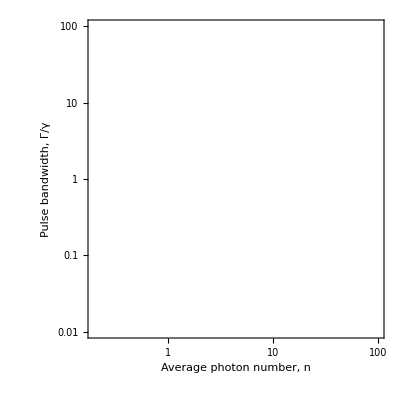

```mathematica
classicalqBhatLongRangePlot=ContourPlot[
p0/.t->s/.s->7γ/.γ->1/.n->nn,{nn,0.,10^2},{Γ,10^-2,10^2},
ColorFunction->ColorData[{"TemperatureMap","Reverse"}],
PlotPoints->300,
ScalingFunctions->{"Log","Log"},
FrameTicksStyle->Directive["Times",FontSize->20,Black],
FrameLabel->{Style["Average photon number, n",20,Black],Style["Pulse bandwidth, Γ/γ",20,Black]},
PlotLegends->BarLegend[Automatic,LegendLabel->"ℬ_q",LabelStyle->{"Times",Black,FontSize->20}],
Epilog->Inset[alphabetlabel[[1]],{0.2,5}]]
```

### Restricted bugdet range

```mathematica
classicalqBhatPlot=ContourPlot[
Abs[p0test]^2 /.t->s/.s->10^8 γ/.γ->1/.n->nn/.Γ->ΓΓ,{nn,0.,1.},{Γ,10^-2,10},
ColorFunction->ColorData[{"TemperatureMap","Reverse"}],
PlotPoints->300,
ScalingFunctions->{None,"Log"},
FrameTicksStyle->Directive["Times",FontSize->20,Black],
FrameLabel->{Style["Average photon number, n",20,Black],Style["Pulse bandwidth, Γ/γ",20,Black]},
PlotLegends->BarLegend[Automatic,LegendLabel->"ℬ_q",LabelStyle->{"Times",Black,FontSize->20}],
Epilog->Inset[alphabetlabel[[1]],{0.2,5}]]
```

-Graphics-

```mathematica
quantumqBhat=ContourPlot[
ℬqqs/.γ->1/.n->nn/.Γ->ΓΓ,{nn,0.,1.},{Γ,10^-2,10},
ColorFunction->ColorData[{"TemperatureMap","Reverse"}],
PlotPoints->300,
ScalingFunctions->{None,"Log"},
FrameTicksStyle->Directive["Times",FontSize->20,Black],
FrameLabel->{Style["Average photon number, n",20,Black],Style["Pulse bandwidth, Γ/γ",20,Black]},
PlotLegends->BarLegend[Automatic,LegendLabel->"ℬ_q",LabelStyle->{"Times",Black,FontSize->20}],
Epilog->Inset[alphabetlabel[[2]],{0.2,5}]];

zerolineOfquantumqBhat=ContourPlot[((1-(2 n γ)/(γ+Γ))/.γ->1/.n->nn/.Γ->ΓΓ)==0,{nn,0.,1.},{ΓΓ,10^-2,10},
ContourStyle->{Dashed,AbsoluteThickness[2],White},
PlotPoints->300,
ScalingFunctions->{None,"Log"}];

qBhatqsPlot=Show[quantumqBhat,zerolineOfquantumqBhat]
```

-Graphics-

## V. Mølmer’s method applied to “Energy-efficient quantum non-demolition measurement with a spin-photon interface”

### 0) Pulse shapes

```mathematica
Clear[Γ];
f=(Θ Γ)/(√π)Exp[- (Γ tt)^2]
```

(ⅇ^(-tt^2 Γ^2) Γ Θ)/(√π)

```mathematica
pulseArea=Integrate[(f* f)//cf,{tt,-∞,∞}]
```

(Γ Θ^2)/(√(2 π))

```mathematica
fourierTransf=Integrate[(Exp[-ⅈ ω tt] f)//cf,{tt,-∞,∞}]
```

ⅇ^(-ω^2/(4 Γ^2)) Θ

```mathematica
Quiet@Manipulate[ListLinePlot[Chop@Quiet@Table[{ΓΓ,fourierTransf/.Θ->1/.Γ->ΓΓ},{t,-20,20,0.2}],PlotRange->All],{ΓΓ,0.1,1,0.1}]
```

NIntegrate::precw: The precision of the argument function (0.948683 ⅇ^(10. (0.9+2 ⅈ ω)) √n) is less than WorkingPrecision (26.).

NIntegrate::inumrexpr: Expression {0.94868329805051376801827701 √n} derived from integrand 0.94868329805051376801827701 2.7182818284590452353602875^(10. (0.90000000000000002220446049+2 ⅈ ω)) √n has evaluated to non-numerical values for all sampling points in the region with boundaries {{-374.80991810185595036709897,-0.0026680190456652920921538721}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

NIntegrate::inumr: The integrand 0.94868329805051376801827701 2.7182818284590452353602875^(10. (0.90000000000000002220446049+2 ⅈ ω)) √n has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0}}.

NIntegrate::precw: The precision of the argument function (0.948683 ⅇ^(10. (0.9+2 ⅈ ω)) √n) is less than WorkingPrecision (26.).

NIntegrate::inumrexpr: Expression {0.94868329805051376801827701 √n} derived from integrand 0.94868329805051376801827701 2.7182818284590452353602875^(10. (0.90000000000000002220446049+2 ⅈ ω)) √n has evaluated to non-numerical values for all sampling points in the region with boundaries {{-374.80991810185595036709897,-0.0026680190456652920921538721}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

NIntegrate::inumr: The integrand 0.94868329805051376801827701 2.7182818284590452353602875^(10. (0.90000000000000002220446049+2 ⅈ ω)) √n has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0}}.

NIntegrate::precw: The precision of the argument function (0.948683 ⅇ^(10. (0.9+2 ⅈ ω)) √n) is less than WorkingPrecision (26.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::inumrexpr: Expression {0.94868329805051376801827701 √n} derived from integrand 0.94868329805051376801827701 2.7182818284590452353602875^(10. (0.90000000000000002220446049+2 ⅈ ω)) √n has evaluated to non-numerical values for all sampling points in the region with boundaries {{-374.80991810185595036709897,-0.0026680190456652920921538721}}.

General::stop: Further output of NIntegrate::inumrexpr will be suppressed during this calculation.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

NIntegrate::inumr: The integrand 0.94868329805051376801827701 2.7182818284590452353602875^(10. (0.90000000000000002220446049+2 ⅈ ω)) √n has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {7.3631889682445511833001547×10^223}. NIntegrate obtained 2.0345052521660581689190515×10^67183 and 2.0345052521660581689190515×10^67183 for the integral and error estimates.

Integrate::idiv: Integral of 7687.26 ⅇ^((0.+20. ⅈ) ω) √n does not converge on {-∞,∞}.

Integrate::idiv: Integral of 7025.63 ⅇ^((0.+19.8 ⅈ) ω) √n does not converge on {-∞,∞}.

Integrate::idiv: Integral of 6420.94 ⅇ^((0.+19.6 ⅈ) ω) √n does not converge on {-∞,∞}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {7.3631889682445511833001547×10^223}. NIntegrate obtained 2.0345052521660581689190515×10^67183 and 2.0345052521660581689190515×10^67183 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (0.948683 ⅇ^(10. (0.9+2 ⅈ ω)) √n) is less than WorkingPrecision (26.).

NIntegrate::inumrexpr: Expression {0.94868329805051376801827701 √n} derived from integrand 0.94868329805051376801827701 2.7182818284590452353602875^(10. (0.90000000000000002220446049+2 ⅈ ω)) √n has evaluated to non-numerical values for all sampling points in the region with boundaries {{-374.80991810185595036709897,-0.0026680190456652920921538721}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

NIntegrate::inumr: The integrand 0.94868329805051376801827701 2.7182818284590452353602875^(10. (0.90000000000000002220446049+2 ⅈ ω)) √n has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0}}.

NIntegrate::precw: The precision of the argument function (0.948683 ⅇ^(10. (0.9+2 ⅈ ω)) √n) is less than WorkingPrecision (26.).

NIntegrate::inumrexpr: Expression {0.94868329805051376801827701 √n} derived from integrand 0.94868329805051376801827701 2.7182818284590452353602875^(10. (0.90000000000000002220446049+2 ⅈ ω)) √n has evaluated to non-numerical values for all sampling points in the region with boundaries {{-374.80991810185595036709897,-0.0026680190456652920921538721}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

NIntegrate::inumr: The integrand 0.94868329805051376801827701 2.7182818284590452353602875^(10. (0.90000000000000002220446049+2 ⅈ ω)) √n has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0}}.

NIntegrate::precw: The precision of the argument function (0.948683 ⅇ^(10. (0.9+2 ⅈ ω)) √n) is less than WorkingPrecision (26.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::inumrexpr: Expression {0.94868329805051376801827701 √n} derived from integrand 0.94868329805051376801827701 2.7182818284590452353602875^(10. (0.90000000000000002220446049+2 ⅈ ω)) √n has evaluated to non-numerical values for all sampling points in the region with boundaries {{-374.80991810185595036709897,-0.0026680190456652920921538721}}.

General::stop: Further output of NIntegrate::inumrexpr will be suppressed during this calculation.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

NIntegrate::inumr: The integrand 0.94868329805051376801827701 2.7182818284590452353602875^(10. (0.90000000000000002220446049+2 ⅈ ω)) √n has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {7.3631889682445511833001547×10^223}. NIntegrate obtained 2.0345052521660581689190515×10^67183 and 2.0345052521660581689190515×10^67183 for the integral and error estimates.

Integrate::idiv: Integral of 7687.26 ⅇ^((0.+20. ⅈ) ω) √n does not converge on {-∞,∞}.

Integrate::idiv: Integral of 7025.63 ⅇ^((0.+19.8 ⅈ) ω) √n does not converge on {-∞,∞}.

Integrate::idiv: Integral of 6420.94 ⅇ^((0.+19.6 ⅈ) ω) √n does not converge on {-∞,∞}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

```mathematica
Quiet@Manipulate[ListLinePlot[Chop@Quiet@Table[{ω,f/.Θ->1/.Γ->ΓΓ/.Θ->1},{ω,-20,20,0.2}],PlotRange->All],{ΓΓ,0.1,1,0.1}]
```

```mathematica
Assuming[Γ>0,Integrate[f,{tt,-∞,∞}]]
```

Θ

```mathematica
uf = f/(√(1-Integrate[f,{tt,0,t}]))
```

(ⅇ^(-tt^2 Γ^2) Γ Θ)/(√π √(1-1/2 Θ Erf[t Γ]))

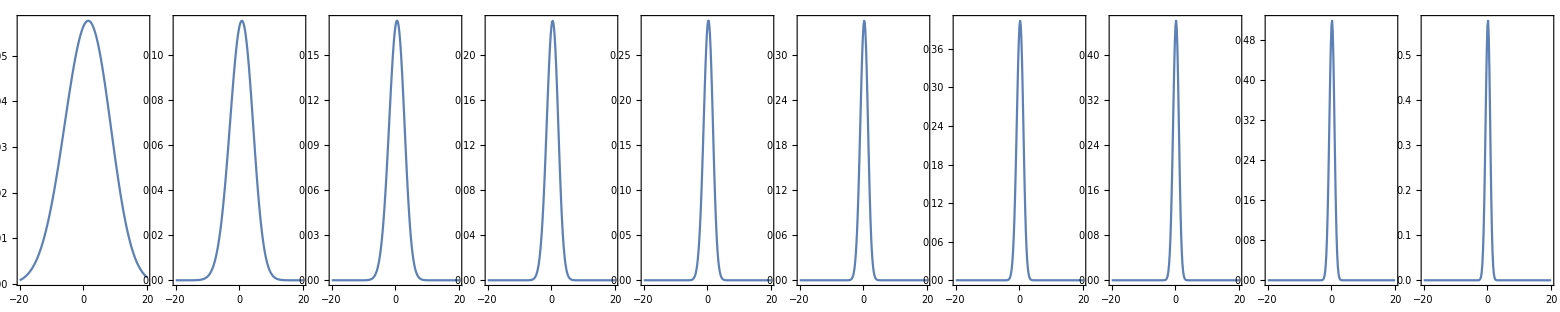

```mathematica
Grid[{Table[ListLinePlot[Chop@Table[{t,uf/.tt->t/.Γ->ΓΓ/.Θ->1},{t,-20,20,0.2}],PlotRange->All],{ΓΓ,0.1,1,0.1}]}]
```

```mathematica
g=√Γ Exp[(-1)^i Γ/2 tt]
```

ⅇ^(1/2 (-1)^i tt Γ) √Γ

```mathematica
Integrate[f^2,{tt,0-∞,∞}]
Integrate[g^2,{tt,0,∞}]
```

(√(Γ^2) Θ^2)/(√(2 π))

(-1)^(1-i)

```mathematica
ug = (g^2/.tt->t)/(1-Integrate[g,{tt,0,t}])//cf
```

Γ^(3/2)/(2 ⅇ^((t Γ)/2)+ⅇ^(t Γ) (-2+√Γ))

```mathematica
ug/.i->0//cf
```

ⅇ^(-(tt Γ)/2)/(√((2 (-1+ⅇ^(-(t Γ)/2)))/Γ^(3/2)+1/Γ))

```mathematica
ug/.i->1//cf
```

ⅇ^(-(tt Γ)/2)/(√((2 (-1+ⅇ^(-(t Γ)/2)))/Γ^(3/2)+1/Γ))

### 1) Hilbert space definition

```mathematica
(*Truncated dimension of the Fock spaces -- for 1 photon in average 10 is more than enough*)
dimFock = 5;
(*Loading bosonic operators*)
LoadBosonicOperators[dimFock]
```

Matrices loaded: 𝕀 (=1), a, 𝕏, ℙ, CoherentState[α], ThermalState[n0]

```mathematica
(*Defining the 4LS subspace*)
dim4LS = 4;
systemsDimensions = {dim4LS,dimFock,dimFock}; (*For partial trace*)
(*defining the basis vectors*)
trionUp = Basis[dim4LS,1]//mf;
trionDw = Basis[dim4LS,2]//mf;
spinUp = Basis[dim4LS,3]//mf;
spinDw = Basis[dim4LS,4]//mf;
```

(1
0
0
0)

(0
1
0
0)

(0
0
1
0)

(0
0
0
1)

```mathematica
(*Defining the dipole operators in the R and L subspaces.*)
σR = out[spinUp,trionUp]//mf;
σL = out[spinDw,trionDw]//mf;

(*Total coherence operator*)
σUpDw = out[spinUp,spinDw]+out[trionUp,trionDw]//mf;

(*Coherence ONLY in the spin subspace σx basically*)
σxspin = out[spinUp,spinDw]+out[spinDw,spinUp]//mf;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0)

(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

Building the total Hilbert space as ℋ = ℋ_(4LS)⊗ ℋ_L⊗ ℋ_R:

```mathematica
(*Dipole operators in the total Hilber space*)
ΣR = kron[σR,𝕀,𝕀];
ΣL= kron[σL,𝕀,𝕀];

(*Left and Right circular polarized photons annihilation operators*)
𝕒L = kron[Eye[dim4LS],a,𝕀];
𝕒R = kron[Eye[dim4LS],𝕀,a];

(*Fock basis*)
numberState[n_]:=Basis[dimFock,n+1];
jointState[ket4LS_,ketL_,ketR_]:= kron[out[ket4LS,ket4LS],out[ketL,ketL],out[ketR,ketR]]
```

```mathematica
ψsp=Normalize[spinDw+spinUp]//mf;(*Equal superposition of up and down in the ground state*)
ψL1photontest =a†.numberState[0];
ψR1photontest=a†.numberState[0];

ψL1coherenttest =CoherentState[1];
ψR1coherenttest =CoherentState[1];
```

(0
0
1/(√2)
1/(√2))

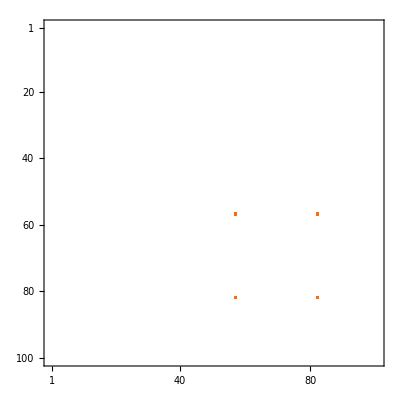

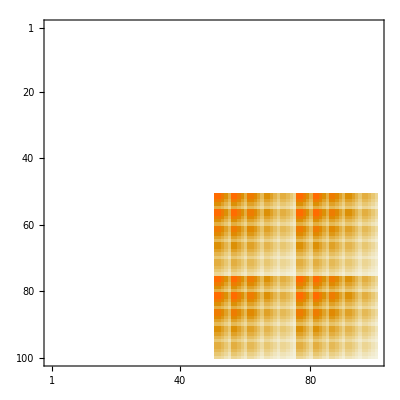

```mathematica
test1photon=jointState[ψsp,ψL1photontest,ψR1photontest];
test1coherent=jointState[ψsp,ψL1coherenttest,ψR1coherenttest];
MatrixPlot@test1photon
MatrixPlot@test1coherent
```

```mathematica
Tr[test1photon]
Tr[test1coherent]//N(*The trace being very close 1 means that eveything is fine with the truncated dimension*)
```

1.

0.992694

```mathematica
CoherentState[1]//N//mf;
numberState[1]//N//mf;
```

(0.606531
0.606531
0.428882
0.247615
0.123808)

(0
1.
0
0
0)

```mathematica
(*Vacuum component of the coherent state*)
numberState[0].CoherentState[1]//N
```

0.606531

```mathematica
vacuumComponentCoherentStateList = Table[{α,numberState[0].CoherentState[α]},{α,0.01,6,0.01}];
```

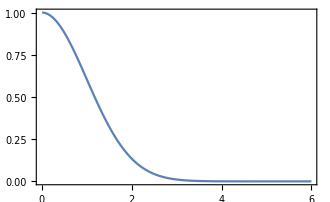

```mathematica
ListLinePlot[%]
```

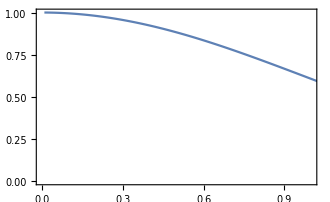

```mathematica
ListLinePlot[%%,PlotRange->{{0,1},All}]
```

### 2) Physical Problem definition

Now I write the code that will evolve the joint state in time following Mølmer’s approach.
We have in to provide in total 8 parameters:
	Pulse parameter:
	1) Γ = Pulse bandwidth (Variable for us).
	System parameters:
	2) γ = excited state decay rate (= 1 for us)
	3) ω0 = system natural frequency
	4) ωs=source natural frequency
	Phenomenological parameters:
	5)ηs = source efficiency = 1 ideally
	6) η = total efficiency =1 ideally. equivalent to a→√η a
	Source and spin phenomenological dephasings: 
	7) γ^⋆=γstar = spin dephasing = 0 ideally
	8) κ^⋆=κstar = light dephasing = 0 ideally

```mathematica
Clear[stateEvolution4LS];

stateEvolution4LS[ρ0_, tf_,Γ_,γ_:1,ω0_:0,ωc_:0,ηs_:1,η_:1,γstar_:0,κstar_:0,Δt_:0.2] := Module[{ρt,TimeDependentRatesTable, TimeDependentHamiltonianTable,len,ℒt,ρUnvect ,ρsp},
(*Vectorize the initial state*)
Print[1];
ρt = Vec[ρ0];
Print[2];
(*Start a list keeping the times and the joint state at that time*)
ρlist = {{0,ρ0}};
Print[3];
(*Start a list keeping the times and the 4LS state at that time*)
(*ρ4LSlist={{0,PTr[ρ0,{2,3},systemsDimensions]}};*)
Print[4];
(*Make a list with all the time dependent rates, the first argument is the spontaneous emission γ, the second is the rate itself, for the case of an exponential decay it reduces to Γ, BUT IT CAN BE ANY FUNCTION OF t (constant for a decreasing pulse*)
Print[5];
TimeDependentRatesTable= Table[{γ, Γ}, {t, 0, tf, Δt}];
Print[6];
(*Make a list of the time dependent Hamiltonians, for each time the Hamiltonian will have a definite value*)

TimeDependentHamiltonianTable =Table[ ω0(ΣR†.ΣR+ΣL†.ΣL) + ωc η( 𝕒R†.𝕒R+𝕒L†.𝕒L)-ⅈ/2 √(γ Γ)√η(ΣR†.𝕒R - ΣR.𝕒R†+ΣL†.𝕒L - ΣL.𝕒L†), {t, 0, tf, Δt}];

(*Compute the length of this list*)
len = Length[TimeDependentHamiltonianTable];

(*The following Do evolves the joint state in time*)

Do[
(*Compute the vectorized Liouvillian with time indexed by k*)
ℒt = 
UnitaryToVec[TimeDependentHamiltonianTable⟦k⟧](*Unitary evolution*)
+LindbladToVec[√γ ΣR](*Decay in R*)
+LindbladToVec[√γ ΣL](*Decay in L*)
+LindbladToVec[√γstar(ΣR†.ΣR+ΣL†.ΣL)](*Pure dephasing of the 4LS*)
+LindbladToVec[√(κstar η)(𝕒R†.𝕒R+𝕒L†.𝕒L)];(*Pure dephasing of light*)

(*Evolve the vectorized state by Δt, updating it.*)
ρt = MatrixExp[ℒt Δt,ρt];

(*Unvectorize obtaining the full densityt matrix*)
ρUnvect =Unvec@ρt;
(*Do a partial trace over the field fo obtain the 4LS density matrix*)
(*ρsp =PTr[ρUnvect ,{2,3}, systemsDimensions];*)

(*Print[{k Δt,ρsp//mf};];*)
(*Append to the list the time and density matrix for the joint an the 4LS at this point of time, notice the unvectorization of the ρt*)
AppendTo[ρlist, {k Δt, ρUnvect }],
(*AppendTo[ρ4LSlist, {k Δt, ρsp}],*)
(*Sweep for all times*)
{k, 1, len}];
(*Return the ρ list containing the times and operators*)
ρlist(*{ρlist,ρ4LSlist}*)]

stateEvolution::usage = "Inputs:
  ρ0 = joint field and system initial state density matrix
  Δt= time step, 
  tf= the final time the physical ORDERED parameters 
  {ω0, ωcav, γ}= atom frequency, cavity frequency and decay rate";
```

```mathematica
Γ=1;
```

```mathematica
(*Light with quantum statistics*)
ψvacuum =kron[numberState[0],numberState[0]];(*vacuum component*)
ψR1photon =kron[numberState[0],a†.numberState[0]];(*one R-photon*)
ψL1photon =kron[a†.numberState[0],numberState[0]];(*one L-photon*)
ψH1photon =(ψR1photon+ψL1photon)/(√2);(*one H-photon*)
ψSuperpositionOfNumberStates[n_]:= (1-n)ψvacuum + n ψH1photon (*Superposition of vacuum and 1 H-photon with the knob "n"*)
```

```mathematica
(*Light with classical statistics*)
ψR1coherent =kron[numberState[0],CoherentState[1/(√2)]];
ψL1coherent =kron[CoherentState[1/(√2)],numberState[0]];
ψH1photoncoh = kron[ψL1coherent,ψR1coherent];
```

```mathematica
(*Sanity chack: are the photonic density matrices normalized?*)
Tr@out[ψH1photon,ψH1photon]
Tr@out[ψH1photoncoh,ψH1photoncoh]//N
```

1.

0.999656

```mathematica
AL=kron[a,𝕀];
AR=kron[𝕀,a];
AH=(AL+AR)/(√2);
```

```mathematica
test=AH†.kron[numberState[0],numberState[0]]
ψH1photon
```

SparseArray[…]

SparseArray[…]

```mathematica
ψH1photon==test
```

True

```mathematica
out[ψH1photoncoh,ψH1photoncoh]//Dimensions
```

{625,625}

```mathematica
ψsp=Normalize[spinDw+spinUp]//N;
ρ0Hqs = kron[out[ψsp,ψsp],out[ψH1photon,ψH1photon]];
ρ0Hcs = kron[out[ψsp,ψsp],out[ψH1photoncoh,ψH1photoncoh]]//N;
```

```mathematica
PTr[ρ0Hcs,{2},{4,625^2}]//mf
```

$Aborted

```mathematica
PrettyTiming[ρtotalCSList=stateEvolution4LS[ρ0Hcs, 25,Γ]];
```

1

2

3

4

5

6

MatrixExp::lslc: Coefficient matrix and target vector(s) or matrix do not have the same dimensions.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[MatrixExp[SparseArray[Automatic,«2»,{1,{{0,«9999»,27246},{«1»}},{-0.2+0. ⅈ,-0.1+0. ⅈ,-0.1+0. ⅈ,-0.2+0. ⅈ,-0.141421+0. ⅈ,-0.1+0. ⅈ,-0.2+0. ⅈ,«27232»,0.+0. ⅈ,0.2+0. ⅈ,0.2+0. ⅈ,0.2+0. ⅈ,0.+0. ⅈ,0.2+0. ⅈ,0.2+0. ⅈ}}],«1»],«1»].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

0h : 0m : 2s

```mathematica
excitationoperator = out[trionUp,trionUp]+out[trionDw,trionDw]
```

SparseArray[…]

```mathematica
tableCS=Table[{ρspCSList[[k,1]],Abs@Chop@Tr[σUpDw.ρspCSList[[k,2]]]},{k,1,Length@ρspCSList}];
tableQS=Table[{ρspQSList[[k,1]],Abs@Chop@Tr[σUpDw.ρspQSList[[k,2]]]},{k,1,Length@ρspQSList}];
```

```mathematica
tableCSσx=Table[{ρspCSList[[k,1]],(Abs@Chop@Tr[σxspin.ρspCSList[[k,2]]])},{k,1,Length@ρspCSList}];
tableQSσx=Table[{ρspQSList[[k,1]],(Abs@Chop@Tr[σxspin.ρspQSList[[k,2]]])},{k,1,Length@ρspQSList}];
```

```mathematica
tableCSσUpDw=Table[{ρspCSList[[k,1]],(Abs@Chop@Tr[σUpDw.ρspCSList[[k,2]]])},{k,1,Length@ρspCSList}];
tableQSσUpDw=Table[{ρspQSList[[k,1]],(Abs@Chop@Tr[σUpDw.ρspQSList[[k,2]]])},{k,1,Length@ρspQSList}];
```

```mathematica
tableCSexc=Table[{ρspCSList[[k,1]],(Chop@Tr[excitationoperator.ρspCSList[[k,2]]])},{k,1,Length@ρspCSList}];
tableQSexc=Table[{ρspQSList[[k,1]],(Chop@Tr[excitationoperator.ρspQSList[[k,2]]])},{k,1,Length@ρspQSList}];
```

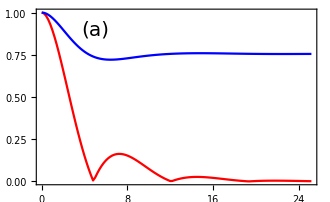

```mathematica
spinCoherence=ListLinePlot[{tableQSσx,tableCSσx},
PlotStyle->{Red,Blue},
Epilog->Inset[Style[alphabetlabel[[1]],20],{5,0.9}],
(*PlotLegends->legend[{"n=1_H","α=1_H"},{0.8,0.78}],*)
PlotRange->All]
```

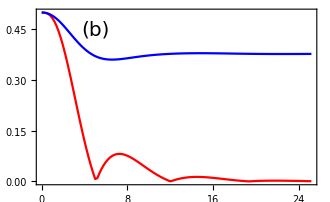

```mathematica
totalCoherence=ListLinePlot[{tableQSσUpDw,tableCSσUpDw},
PlotStyle->{Red,Blue},
Epilog->Inset[Style[alphabetlabel[[2]],20],{5,0.45}],
(*PlotLegends->legend[{"n=1_H","α=1_H"},{0.8,0.78}],*)
PlotRange->All]
```

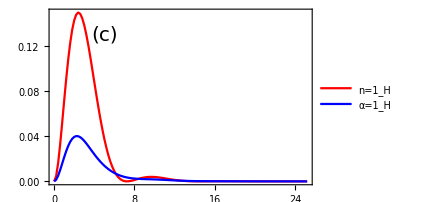

```mathematica
excitationplot=ListLinePlot[{tableQSexc,tableCSexc},
PlotStyle->{Red,Blue},
Epilog->Inset[Style[alphabetlabel[[3]],20],{5,0.13}],
PlotLegends->legend[{"n=1_H","α=1_H"},{0.8,0.77}],
PlotRange->All]
```

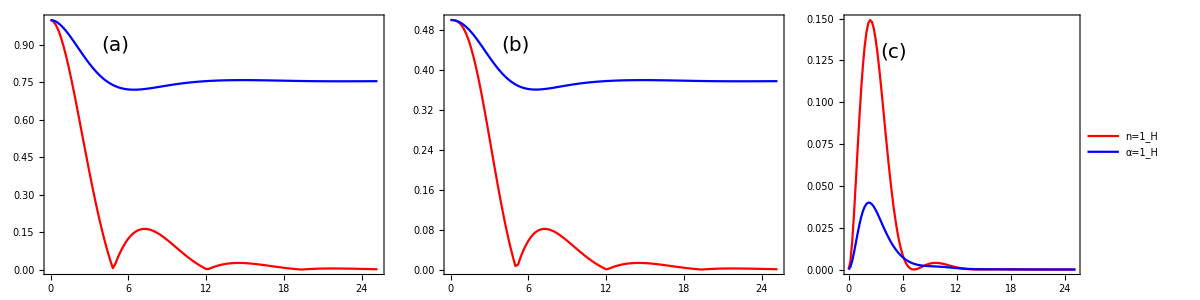

```mathematica
Grid[{{spinCoherence,totalCoherence,excitationplot}}]
```

### Understanding the partial trace function

To use the σUpDw I’ll have to trace over the field. This is accomplished via the partial trace PTr implemented in melt! Its usage is as follows:

```mathematica
(* ρ = |Subscript[ψ, 1]⟩⟨Subscript[ψ, 1]|⊗|Subscript[ψ, 2]⟩⟨Subscript[ψ, 2]| *)
ψ1 = {1,1}//Normalize;
ψ2 = {2,ⅈ,1,4}//Normalize;
ψ3 = {4,-5ⅈ,1}//Normalize;
ρ = kron[out[ψ1,ψ1],out[ψ2,ψ2],out[ψ3,ψ3]]//N//mf;
```

(0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.-0.017316 ⅈ | 0.021645 | 0.-0.004329 ⅈ | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.0692641 | 0.+0.0865801 ⅈ | 0.017316 | 0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.-0.017316 ⅈ | 0.021645 | 0.-0.004329 ⅈ | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.0692641 | 0.+0.0865801 ⅈ | 0.017316
0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | -0.021645 | 0.-0.0270563 ⅈ | -0.00541126 | 0.-0.021645 ⅈ | 0.0270563 | 0.-0.00541126 ⅈ | 0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ | 0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | -0.021645 | 0.-0.0270563 ⅈ | -0.00541126 | 0.-0.021645 ⅈ | 0.0270563 | 0.-0.00541126 ⅈ | 0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ
0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.-0.004329 ⅈ | 0.00541126 | 0.-0.00108225 ⅈ | 0.004329 | 0.+0.00541126 ⅈ | 0.00108225 | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.-0.004329 ⅈ | 0.00541126 | 0.-0.00108225 ⅈ | 0.004329 | 0.+0.00541126 ⅈ | 0.00108225 | 0.017316 | 0.+0.021645 ⅈ | 0.004329
0.+0.017316 ⅈ | -0.021645 | 0.+0.004329 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.+0.00865801 ⅈ | -0.0108225 | 0.+0.0021645 ⅈ | 0.+0.034632 ⅈ | -0.04329 | 0.+0.00865801 ⅈ | 0.+0.017316 ⅈ | -0.021645 | 0.+0.004329 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.+0.00865801 ⅈ | -0.0108225 | 0.+0.0021645 ⅈ | 0.+0.034632 ⅈ | -0.04329 | 0.+0.00865801 ⅈ
0.021645 | 0.+0.0270563 ⅈ | 0.00541126 | 0.-0.0108225 ⅈ | 0.0135281 | 0.-0.00270563 ⅈ | 0.0108225 | 0.+0.0135281 ⅈ | 0.00270563 | 0.04329 | 0.+0.0541126 ⅈ | 0.0108225 | 0.021645 | 0.+0.0270563 ⅈ | 0.00541126 | 0.-0.0108225 ⅈ | 0.0135281 | 0.-0.00270563 ⅈ | 0.0108225 | 0.+0.0135281 ⅈ | 0.00270563 | 0.04329 | 0.+0.0541126 ⅈ | 0.0108225
0.+0.004329 ⅈ | -0.00541126 | 0.+0.00108225 ⅈ | 0.0021645 | 0.+0.00270563 ⅈ | 0.000541126 | 0.+0.0021645 ⅈ | -0.00270563 | 0.+0.000541126 ⅈ | 0.+0.00865801 ⅈ | -0.0108225 | 0.+0.0021645 ⅈ | 0.+0.004329 ⅈ | -0.00541126 | 0.+0.00108225 ⅈ | 0.0021645 | 0.+0.00270563 ⅈ | 0.000541126 | 0.+0.0021645 ⅈ | -0.00270563 | 0.+0.000541126 ⅈ | 0.+0.00865801 ⅈ | -0.0108225 | 0.+0.0021645 ⅈ
0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.-0.00865801 ⅈ | 0.0108225 | 0.-0.0021645 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.-0.00865801 ⅈ | 0.0108225 | 0.-0.0021645 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.034632 | 0.+0.04329 ⅈ | 0.00865801
0.-0.021645 ⅈ | 0.0270563 | 0.-0.00541126 ⅈ | -0.0108225 | 0.-0.0135281 ⅈ | -0.00270563 | 0.-0.0108225 ⅈ | 0.0135281 | 0.-0.00270563 ⅈ | 0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | 0.-0.021645 ⅈ | 0.0270563 | 0.-0.00541126 ⅈ | -0.0108225 | 0.-0.0135281 ⅈ | -0.00270563 | 0.-0.0108225 ⅈ | 0.0135281 | 0.-0.00270563 ⅈ | 0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ
0.004329 | 0.+0.00541126 ⅈ | 0.00108225 | 0.-0.0021645 ⅈ | 0.00270563 | 0.-0.000541126 ⅈ | 0.0021645 | 0.+0.00270563 ⅈ | 0.000541126 | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.004329 | 0.+0.00541126 ⅈ | 0.00108225 | 0.-0.0021645 ⅈ | 0.00270563 | 0.-0.000541126 ⅈ | 0.0021645 | 0.+0.00270563 ⅈ | 0.000541126 | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645
0.0692641 | 0.+0.0865801 ⅈ | 0.017316 | 0.-0.034632 ⅈ | 0.04329 | 0.-0.00865801 ⅈ | 0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.138528 | 0.+0.17316 ⅈ | 0.034632 | 0.0692641 | 0.+0.0865801 ⅈ | 0.017316 | 0.-0.034632 ⅈ | 0.04329 | 0.-0.00865801 ⅈ | 0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.138528 | 0.+0.17316 ⅈ | 0.034632
0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ | -0.04329 | 0.-0.0541126 ⅈ | -0.0108225 | 0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | 0.-0.17316 ⅈ | 0.21645 | 0.-0.04329 ⅈ | 0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ | -0.04329 | 0.-0.0541126 ⅈ | -0.0108225 | 0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | 0.-0.17316 ⅈ | 0.21645 | 0.-0.04329 ⅈ
0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.-0.00865801 ⅈ | 0.0108225 | 0.-0.0021645 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.-0.00865801 ⅈ | 0.0108225 | 0.-0.0021645 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.034632 | 0.+0.04329 ⅈ | 0.00865801
0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.-0.017316 ⅈ | 0.021645 | 0.-0.004329 ⅈ | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.0692641 | 0.+0.0865801 ⅈ | 0.017316 | 0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.-0.017316 ⅈ | 0.021645 | 0.-0.004329 ⅈ | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.0692641 | 0.+0.0865801 ⅈ | 0.017316
0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | -0.021645 | 0.-0.0270563 ⅈ | -0.00541126 | 0.-0.021645 ⅈ | 0.0270563 | 0.-0.00541126 ⅈ | 0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ | 0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | -0.021645 | 0.-0.0270563 ⅈ | -0.00541126 | 0.-0.021645 ⅈ | 0.0270563 | 0.-0.00541126 ⅈ | 0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ
0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.-0.004329 ⅈ | 0.00541126 | 0.-0.00108225 ⅈ | 0.004329 | 0.+0.00541126 ⅈ | 0.00108225 | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.-0.004329 ⅈ | 0.00541126 | 0.-0.00108225 ⅈ | 0.004329 | 0.+0.00541126 ⅈ | 0.00108225 | 0.017316 | 0.+0.021645 ⅈ | 0.004329
0.+0.017316 ⅈ | -0.021645 | 0.+0.004329 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.+0.00865801 ⅈ | -0.0108225 | 0.+0.0021645 ⅈ | 0.+0.034632 ⅈ | -0.04329 | 0.+0.00865801 ⅈ | 0.+0.017316 ⅈ | -0.021645 | 0.+0.004329 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.+0.00865801 ⅈ | -0.0108225 | 0.+0.0021645 ⅈ | 0.+0.034632 ⅈ | -0.04329 | 0.+0.00865801 ⅈ
0.021645 | 0.+0.0270563 ⅈ | 0.00541126 | 0.-0.0108225 ⅈ | 0.0135281 | 0.-0.00270563 ⅈ | 0.0108225 | 0.+0.0135281 ⅈ | 0.00270563 | 0.04329 | 0.+0.0541126 ⅈ | 0.0108225 | 0.021645 | 0.+0.0270563 ⅈ | 0.00541126 | 0.-0.0108225 ⅈ | 0.0135281 | 0.-0.00270563 ⅈ | 0.0108225 | 0.+0.0135281 ⅈ | 0.00270563 | 0.04329 | 0.+0.0541126 ⅈ | 0.0108225
0.+0.004329 ⅈ | -0.00541126 | 0.+0.00108225 ⅈ | 0.0021645 | 0.+0.00270563 ⅈ | 0.000541126 | 0.+0.0021645 ⅈ | -0.00270563 | 0.+0.000541126 ⅈ | 0.+0.00865801 ⅈ | -0.0108225 | 0.+0.0021645 ⅈ | 0.+0.004329 ⅈ | -0.00541126 | 0.+0.00108225 ⅈ | 0.0021645 | 0.+0.00270563 ⅈ | 0.000541126 | 0.+0.0021645 ⅈ | -0.00270563 | 0.+0.000541126 ⅈ | 0.+0.00865801 ⅈ | -0.0108225 | 0.+0.0021645 ⅈ
0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.-0.00865801 ⅈ | 0.0108225 | 0.-0.0021645 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.-0.00865801 ⅈ | 0.0108225 | 0.-0.0021645 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.034632 | 0.+0.04329 ⅈ | 0.00865801
0.-0.021645 ⅈ | 0.0270563 | 0.-0.00541126 ⅈ | -0.0108225 | 0.-0.0135281 ⅈ | -0.00270563 | 0.-0.0108225 ⅈ | 0.0135281 | 0.-0.00270563 ⅈ | 0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | 0.-0.021645 ⅈ | 0.0270563 | 0.-0.00541126 ⅈ | -0.0108225 | 0.-0.0135281 ⅈ | -0.00270563 | 0.-0.0108225 ⅈ | 0.0135281 | 0.-0.00270563 ⅈ | 0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ
0.004329 | 0.+0.00541126 ⅈ | 0.00108225 | 0.-0.0021645 ⅈ | 0.00270563 | 0.-0.000541126 ⅈ | 0.0021645 | 0.+0.00270563 ⅈ | 0.000541126 | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.004329 | 0.+0.00541126 ⅈ | 0.00108225 | 0.-0.0021645 ⅈ | 0.00270563 | 0.-0.000541126 ⅈ | 0.0021645 | 0.+0.00270563 ⅈ | 0.000541126 | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645
0.0692641 | 0.+0.0865801 ⅈ | 0.017316 | 0.-0.034632 ⅈ | 0.04329 | 0.-0.00865801 ⅈ | 0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.138528 | 0.+0.17316 ⅈ | 0.034632 | 0.0692641 | 0.+0.0865801 ⅈ | 0.017316 | 0.-0.034632 ⅈ | 0.04329 | 0.-0.00865801 ⅈ | 0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.138528 | 0.+0.17316 ⅈ | 0.034632
0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ | -0.04329 | 0.-0.0541126 ⅈ | -0.0108225 | 0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | 0.-0.17316 ⅈ | 0.21645 | 0.-0.04329 ⅈ | 0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ | -0.04329 | 0.-0.0541126 ⅈ | -0.0108225 | 0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | 0.-0.17316 ⅈ | 0.21645 | 0.-0.04329 ⅈ
0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.-0.00865801 ⅈ | 0.0108225 | 0.-0.0021645 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.-0.00865801 ⅈ | 0.0108225 | 0.-0.0021645 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.034632 | 0.+0.04329 ⅈ | 0.00865801)

```mathematica
PTr[ρ,{1,3},{2,4,3}]//mf;
out[ψ2,ψ2]//N//mf;
```

(0.181818 | 0.-0.0909091 ⅈ | 0.0909091 | 0.363636
0.+0.0909091 ⅈ | 0.0454545 | 0.+0.0454545 ⅈ | 0.+0.181818 ⅈ
0.0909091 | 0.-0.0454545 ⅈ | 0.0454545 | 0.181818
0.363636 | 0.-0.181818 ⅈ | 0.181818 | 0.727273)

(0.181818 | 0.-0.0909091 ⅈ | 0.0909091 | 0.363636
0.+0.0909091 ⅈ | 0.0454545 | 0.+0.0454545 ⅈ | 0.+0.181818 ⅈ
0.0909091 | 0.-0.0454545 ⅈ | 0.0454545 | 0.181818
0.363636 | 0.-0.181818 ⅈ | 0.181818 | 0.727273)

```mathematica
PTr[ρ,{1,2},{2,4,3}]//mf;
out[ψ3,ψ3]//N//mf;
```

(0.380952 | 0.+0.47619 ⅈ | 0.0952381
0.-0.47619 ⅈ | 0.595238 | 0.-0.119048 ⅈ
0.0952381 | 0.+0.119048 ⅈ | 0.0238095)

(0.380952 | 0.+0.47619 ⅈ | 0.0952381
0.-0.47619 ⅈ | 0.595238 | 0.-0.119048 ⅈ
0.0952381 | 0.+0.119048 ⅈ | 0.0238095)

```mathematica
PTr[ρ,{1},{2,4,3}]//mf;
kron[out[ψ2,ψ2],out[ψ3,ψ3]]//N//mf;
```

(0.0692641 | 0.+0.0865801 ⅈ | 0.017316 | 0.-0.034632 ⅈ | 0.04329 | 0.-0.00865801 ⅈ | 0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.138528 | 0.+0.17316 ⅈ | 0.034632
0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ | -0.04329 | 0.-0.0541126 ⅈ | -0.0108225 | 0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | 0.-0.17316 ⅈ | 0.21645 | 0.-0.04329 ⅈ
0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.-0.00865801 ⅈ | 0.0108225 | 0.-0.0021645 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.034632 | 0.+0.04329 ⅈ | 0.00865801
0.+0.034632 ⅈ | -0.04329 | 0.+0.00865801 ⅈ | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.+0.017316 ⅈ | -0.021645 | 0.+0.004329 ⅈ | 0.+0.0692641 ⅈ | -0.0865801 | 0.+0.017316 ⅈ
0.04329 | 0.+0.0541126 ⅈ | 0.0108225 | 0.-0.021645 ⅈ | 0.0270563 | 0.-0.00541126 ⅈ | 0.021645 | 0.+0.0270563 ⅈ | 0.00541126 | 0.0865801 | 0.+0.108225 ⅈ | 0.021645
0.+0.00865801 ⅈ | -0.0108225 | 0.+0.0021645 ⅈ | 0.004329 | 0.+0.00541126 ⅈ | 0.00108225 | 0.+0.004329 ⅈ | -0.00541126 | 0.+0.00108225 ⅈ | 0.+0.017316 ⅈ | -0.021645 | 0.+0.004329 ⅈ
0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.-0.017316 ⅈ | 0.021645 | 0.-0.004329 ⅈ | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.0692641 | 0.+0.0865801 ⅈ | 0.017316
0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | -0.021645 | 0.-0.0270563 ⅈ | -0.00541126 | 0.-0.021645 ⅈ | 0.0270563 | 0.-0.00541126 ⅈ | 0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ
0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.-0.004329 ⅈ | 0.00541126 | 0.-0.00108225 ⅈ | 0.004329 | 0.+0.00541126 ⅈ | 0.00108225 | 0.017316 | 0.+0.021645 ⅈ | 0.004329
0.138528 | 0.+0.17316 ⅈ | 0.034632 | 0.-0.0692641 ⅈ | 0.0865801 | 0.-0.017316 ⅈ | 0.0692641 | 0.+0.0865801 ⅈ | 0.017316 | 0.277056 | 0.+0.34632 ⅈ | 0.0692641
0.-0.17316 ⅈ | 0.21645 | 0.-0.04329 ⅈ | -0.0865801 | 0.-0.108225 ⅈ | -0.021645 | 0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ | 0.-0.34632 ⅈ | 0.4329 | 0.-0.0865801 ⅈ
0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.-0.017316 ⅈ | 0.021645 | 0.-0.004329 ⅈ | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.0692641 | 0.+0.0865801 ⅈ | 0.017316)

(0.0692641 | 0.+0.0865801 ⅈ | 0.017316 | 0.-0.034632 ⅈ | 0.04329 | 0.-0.00865801 ⅈ | 0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.138528 | 0.+0.17316 ⅈ | 0.034632
0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ | -0.04329 | 0.-0.0541126 ⅈ | -0.0108225 | 0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | 0.-0.17316 ⅈ | 0.21645 | 0.-0.04329 ⅈ
0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.-0.00865801 ⅈ | 0.0108225 | 0.-0.0021645 ⅈ | 0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.034632 | 0.+0.04329 ⅈ | 0.00865801
0.+0.034632 ⅈ | -0.04329 | 0.+0.00865801 ⅈ | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.+0.017316 ⅈ | -0.021645 | 0.+0.004329 ⅈ | 0.+0.0692641 ⅈ | -0.0865801 | 0.+0.017316 ⅈ
0.04329 | 0.+0.0541126 ⅈ | 0.0108225 | 0.-0.021645 ⅈ | 0.0270563 | 0.-0.00541126 ⅈ | 0.021645 | 0.+0.0270563 ⅈ | 0.00541126 | 0.0865801 | 0.+0.108225 ⅈ | 0.021645
0.+0.00865801 ⅈ | -0.0108225 | 0.+0.0021645 ⅈ | 0.004329 | 0.+0.00541126 ⅈ | 0.00108225 | 0.+0.004329 ⅈ | -0.00541126 | 0.+0.00108225 ⅈ | 0.+0.017316 ⅈ | -0.021645 | 0.+0.004329 ⅈ
0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.-0.017316 ⅈ | 0.021645 | 0.-0.004329 ⅈ | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.0692641 | 0.+0.0865801 ⅈ | 0.017316
0.-0.04329 ⅈ | 0.0541126 | 0.-0.0108225 ⅈ | -0.021645 | 0.-0.0270563 ⅈ | -0.00541126 | 0.-0.021645 ⅈ | 0.0270563 | 0.-0.00541126 ⅈ | 0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ
0.00865801 | 0.+0.0108225 ⅈ | 0.0021645 | 0.-0.004329 ⅈ | 0.00541126 | 0.-0.00108225 ⅈ | 0.004329 | 0.+0.00541126 ⅈ | 0.00108225 | 0.017316 | 0.+0.021645 ⅈ | 0.004329
0.138528 | 0.+0.17316 ⅈ | 0.034632 | 0.-0.0692641 ⅈ | 0.0865801 | 0.-0.017316 ⅈ | 0.0692641 | 0.+0.0865801 ⅈ | 0.017316 | 0.277056 | 0.+0.34632 ⅈ | 0.0692641
0.-0.17316 ⅈ | 0.21645 | 0.-0.04329 ⅈ | -0.0865801 | 0.-0.108225 ⅈ | -0.021645 | 0.-0.0865801 ⅈ | 0.108225 | 0.-0.021645 ⅈ | 0.-0.34632 ⅈ | 0.4329 | 0.-0.0865801 ⅈ
0.034632 | 0.+0.04329 ⅈ | 0.00865801 | 0.-0.017316 ⅈ | 0.021645 | 0.-0.004329 ⅈ | 0.017316 | 0.+0.021645 ⅈ | 0.004329 | 0.0692641 | 0.+0.0865801 ⅈ | 0.017316)

## VI. Poincaré sphere plots

## VII. cBhat plots

#### Interferometer phase optimization

```mathematica
cBhatqs[ϕ_]:=Abs[Cos[ϕ]]
```

```mathematica
cBhatcs[ϕ_]:=(1+√((1+ⅇ)-2 √ⅇ Cosh[Sin[ϕ]/2]))/(√ⅇ)
```

```mathematica
FindMinimum[cBhatcs[ϕ],ϕ]//cf
```

{0.606531,{ϕ→1.5708}}

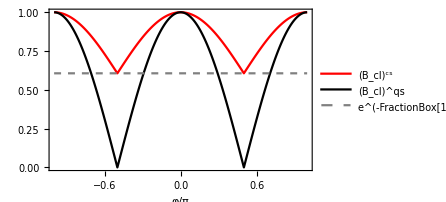

```mathematica
(*Creating the lists to plot*)
cBhatcsList =Table[{ϕ/π, cBhatcs[ϕ]},{ϕ,-π,π,π/100}];
cBhatqsList =Table[{ϕ/π, cBhatqs[ϕ]},{ϕ,-π,π,π/100}];
minimunofcBhatcsList=Table[{ϕ/π, 1/√ⅇ},{ϕ,-π,π,π/100}];

ListLinePlot[{cBhatcsList,cBhatqsList,minimunofcBhatcsList},
PlotStyle->{{Red},{Black},{Gray,Dashed}},
FrameLabel->{"φ/π",None},
PlotLegends->legend[{"(B_cl)^cs","(B_cl)^qs","e^(-FractionBox[1, 2])"},{0.5,0.3}]]
```